# 椭圆曲线

## 离散对数问题(DLP, Discrete Logarithm Problem): 群 G=<a> 中元素 h∈G, 求满足 h=g^m 的整数 m.

称满足 h=g^m 的最小正整数 m 为 h 关于 g 的对数(或指数), 记为 m=log_g(h), 或 m=ind_g(h).
对于任意给定的 h, 对 m 的求解是困难的, 所以被用于加密算法中, 包括密钥交换, 加密, 数字签名和哈希函数.

## Diffie-Hellman 密钥交换

公开信息: 群 G 和其中的 n 阶元 g. 在对称加密中, 信息传输双方需要交换密钥来对信息进行加密. 举例说明甲乙两人交换密钥的过程如下:
1) 甲, 乙分别选择一个不公开的 a, b, 且 0<a<n, 0<b<n.
2) 甲将 g^a发送给乙, 乙将 g^b 发送给甲.
3) 甲将收到的 g^b 计算 a 次幂得到 g^ba, 同样的乙将得到的 g^a 计算 b 次幂得到 g^ab.
则 g^ab 就是甲乙两人的共同私钥, 当第三方要破解私钥时, 将面临离散对数问题, 求解相应的指数 a, b, 这对于比较大的 a,b 来说是非常耗时的.

## 目前, 解决 𝔽_p^* 离散对数问题的较好的算法时间复杂度为 O(ⅇ^(c((log p)(log log p)^2)^(1/3)))

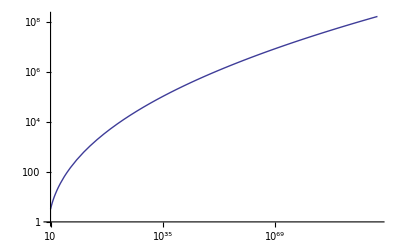

```mathematica
LogLogPlot[ⅇ^((Log[x] Log[Log[x]]^2)^(1/3)),{x,10,10^100}]
```

```mathematica
Manipulate[RegionPlot[y^2≤x^3+A x+B,{x,-5,5},{y,-5,5}],{{A,1},-5,5},{{B,1},-5,5}]
```

```mathematica
EllipticCurve[A_,B_][x_]:=x^3+A x+B
Lambda[A_,B_,p_][P__,Q__]:=If[P==Q ,If[P[[2]]≠0, (3 P[[1]]^2+A)/(2P[[2]]),∞],If[P[[1]]==Q[[1]],∞,(P[[2]]-Q[[2]])/(P[[1]]-Q[[1]])] ]
ESum[A_,B_,p_][P__,Q__]:=If[Lambda [A,B,p][P,Q]==∞,{∞,∞},{(Lambda [A,B,p][P,Q])^2-P[[1]]-Q[[1]],-(Lambda [A,B,p][P,Q])^3+(P[[1]]+Q[[1]])Lambda [A,B,p][P,Q]-(P[[2]]-Lambda [A,B,p][P,Q]P[[1]])}]
```

```mathematica
Prime
```

```mathematica
P={1,2};
Q=ESum[-5,8,9][P,P]
P3=ESum[-5,8,9][P,Q]
P4=ESum[-5,8,9][P3,P]
```

{-7/4,-27/8}

{553/121,-11950/1331}

{45313/11664,8655103/1259712}

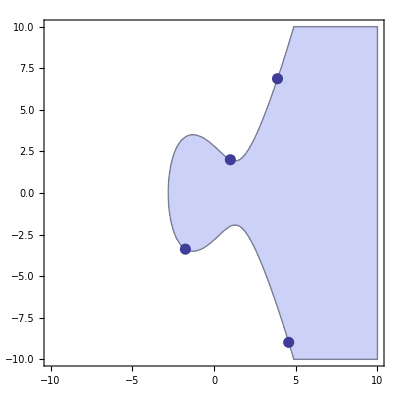

```mathematica
Show[{RegionPlot[y^2≤EllipticCurve[-5,8][x],{x,-10,10},{y,-10,10}],
ListPlot[{P,Q,P3,P4},PlotStyle->PointSize[0.02]]}]
```